```mathematica
ClearAll["Global`*"]
```

```mathematica
eqns=({((1-m)N1+m N2)ⅇ^-z+
(((ⅇ^(-(θ1-x1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2)))*(N1-m N1)+ (((ⅇ^(-(θ1-x2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2)))*m N2))ⅇ^(-β((1-m)N1+m N2)),
((1-m)N2+m N1)ⅇ^-z+
(((ⅇ^(-(θ2-x2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2)))* (N2-m N2)+((ⅇ^(-(θ2-x1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2)))* m N1)ⅇ^(-β((1-m)N2+m N1)),(w1 x1+(1-w1)x2+D[Log[w1(ⅇ^(-(θ1-x1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w1)(ⅇ^(-(θ1-x2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],x1]),
(w2 x2+(1-w2)x1+D[Log[(1-w2)(ⅇ^(-(θ2-x1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+w2(ⅇ^(-(θ2-x2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],x2])}/.{w1->(N1-m N1)/(N1-m N1+m N2),w2->(N2- m N2)/(N2- m N2+m N1)})/.{N1->N1star,N2->N2star,x1->x1star,x2->x2star};
```

```mathematica
Jac=Outer[D,eqns,{N1star,N2star,x1star,x2star}];
```

```mathematica
EvolvingKevinStochastic[Tmax_,z_,rmax_,β_,θ1_,θ2_,initμ1_,initμ2_,τ_,σ_,m_,processerror_]:=Block[{},
(* Initialize variables *)
N1=Array[0&,Tmax+1];
N2=Array[0&,Tmax+1];
x1=Array[0&,Tmax+1];
x2=Array[0&,Tmax+1];
N1[[1]]=2;N2[[1]]=2;x1[[1]]=initμ1;x2[[1]]=initμ2;
(* Trait distributions *)
p1[x_,μ1_]=PDF[NormalDistribution[μ1,σ],x];
p2[x_,μ2_]=PDF[NormalDistribution[μ2,σ],x];

(* Average fitness W of individuals with traits x *)
(* Integrate[α[rmax,x,τ,θ]*(w p1[x,μ1,1]+(1-w)p2[x,μ2,1]),{x,-∞,∞}], then take derivatives with respect to μ1 and μ2 to get *)
meanFit1=D[Log[w(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+(1-w)(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2))],μ1];
meanFit2=D[Log[(1-w)(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))+w(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2))],μ2];

(* Calculate reproductive rates: outside of loop and init for speed *)
(*r1Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site1 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r1Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
(*r2Site2 Integrate[α[rmax,x,τ,θ1](p1[x,μ1,σ]),{x,-∞,∞}]*)
r1Site1=(ⅇ^(-(θ1-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site1=(ⅇ^(-(θ1-μ2)^2/(2 (σ^2+τ^2)))τ rmax)/(√(τ^2+σ^2));r1Site2=(ⅇ^(-(θ2-μ1)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));r2Site2=(ⅇ^(-(θ2-μ2)^2/(2 (σ^2+τ^2))) τ rmax)/(√(τ^2+σ^2));
(* Simulation loop *)
Table[
(* Calculate reprod using mixture distribution after migration *)
r1Site1EQ=r1Site1/.{μ1->x1[[i]]};r2Site1EQ=r2Site1/.{μ2->x2[[i]]};r1Site2EQ=r1Site2/.{μ1->x1[[i]]};r2Site2EQ=r2Site2/.{μ2->x2[[i]]};
(* Find biomass at time t+1 *)
(* It now takes into account the fact that a fraction of the population leaves the site as -m N1[[i]] *)
N1[[i+1]]=
((1-m)N1[[i]]+m N2[[i]])ⅇ^-z+
((r1Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])*(N1[[i]]-m N1[[i]])+ ((r2Site1EQ+RandomVariate[UniformDistribution[{0,processerror}]])*m N2[[i]]))ⅇ^(-β((1-m)N1[[i]]+m N2[[i]])); 
N2[[i+1]]=
((1-m)N2[[i]]+m N1[[i]])ⅇ^-z+
((r2Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* (N2[[i]]-m N2[[i]])+(r1Site2EQ+RandomVariate[UniformDistribution[{0,processerror}]])* m N1[[i]])ⅇ^(-β((1-m)N2[[i]]+m N1[[i]]));
(* Find mean trait value at time t+1 *)
x1[[i+1]]=σ^2(w x1[[i]]+(1-w)x2[[i]]+meanFit1)/.{θ->θ1,μ1->x1[[i]],μ2->x2[[i]],w->(N1[[i]]-m N1[[i]])/(N1[[i]]+m N2[[i]]-m N1[[i]])};
x2[[i+1]]=σ^2(w x2[[i]]+(1-w)x1[[i]]+meanFit2)/.{θ->θ2,μ1->x1[[i]],μ2->x2[[i]],w->(N2[[i]]- m N2[[i]])/(m N1[[i]]+N2[[i]]- m N2[[i]])};
,{i,1,Tmax}];
toplotN1=Table[{i,N1[[i]]},{i,1,Tmax}];
toplotN2=Table[{i,N2[[i]]},{i,1,Tmax}];
toplotx1=Table[{i,x1[[i]]},{i,1,Tmax}];
toplotx2=Table[{i,x2[[i]]},{i,1,Tmax}];

]
```

```mathematica
MinReEig=Table[
out=EvolvingKevinStochastic[
(*Tmax*)tmax=10000,
(*z*)z=0.5,
(*rmax*)rmax=2,
(*β*)β=0.001,
(*θ1*)θ1=5,
(*θ2*)θ2=10,
(*initμ1*)5,
(*initμ2*)10,
(*τ*)τ=1,
(*σ*)σ=1,
(*m*)M,
(*processerror*)0.00
];
burnin=0.9;
N1num=Last[N1];(*Mean[N1[[Floor[tmax*burnin];;tmax]]];*)
N2num=Last[N2];(*Mean[N2[[Floor[tmax*burnin];;tmax]]];*)
x1num=Last[x1];(*Mean[x1[[Floor[tmax*burnin];;tmax]]];*)
x2num=Last[x2];(*Mean[x2[[Floor[tmax*burnin];;tmax]]];*)
JacSpec=Jac/.{N1star->N1num,N2star->N2num,x1star->x1num,x2star->x2num,m->M};
Eig=Eigenvalues[JacSpec];
ReEig = Re[Eig];
ImEig = Im[Eig];
{M,Min[ReEig],Max[ReEig]},
{M,0.2,0.5,0.01}];
```

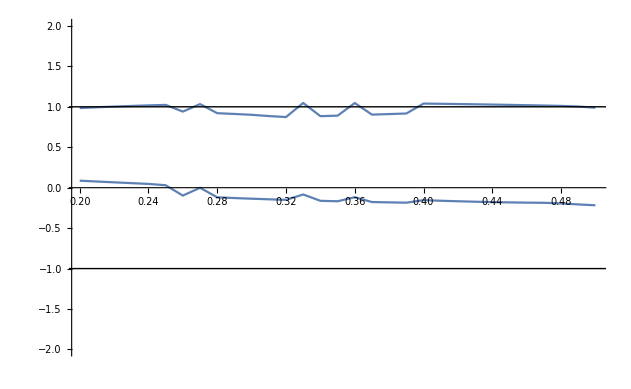

```mathematica
Show[
ListPlot[Transpose[{MinReEig[[All,1]],MinReEig[[All,2]]}],Joined->True,PlotRange->{-2,2}],
ListPlot[Transpose[{MinReEig[[All,1]],MinReEig[[All,3]]}],Joined->True],
Graphics[Line[{{0,1},{1,1}}]],
Graphics[Line[{{0,-1},{1,-1}}]]
]
(*Show[
ListPlot[N1num,Joined->True]
]*)
```

```mathematica
Manipulate[
out=EvolvingKevinStochastic[
(*Tmax*)tmax=10000,
(*z*)z=0.5,
(*rmax*)rmax=2,
(*β*)β=0.001,
(*θ1*)θ1=5,
(*θ2*)θ2=10,
(*initμ1*)5,
(*initμ2*)10,
(*τ*)τ=1,
(*σ*)σ=1,
(*m*)M,
(*processerror*)0.00
];
burnin=0.9;
N1num=Last[N1];(*Mean[N1[[Floor[tmax*burnin];;tmax]]];*)
N2num=Last[N2];(*Mean[N2[[Floor[tmax*burnin];;tmax]]];*)
x1num=Last[x1];(*Mean[x1[[Floor[tmax*burnin];;tmax]]];*)
x2num=Last[x2];(*Mean[x2[[Floor[tmax*burnin];;tmax]]];*)
JacSpec=Jac/.{N1star->N1num,N2star->N2num,x1star->x1num,x2star->x2num,m->M};
Eig=Eigenvalues[JacSpec];
ReEig = Re[Eig];
ImEig = Im[Eig];
Show[
ListPlot[Transpose[{ReEig,ImEig}],Joined->False,PlotRange->{{-2,2},{-2,2}}],
Graphics[Circle[]]
],
{M,0.2,0.5,0.01}]
```